```mathematica
data = Import["Grove_curve_2.csv"]
```

{{0,0.},{0.0104843,509.317},{0.0196011,993.789},{0.0309972,1590.06},{0.0387464,1987.58},{0.0501425,2621.12},{0.0565242,2981.37},{0.0701994,3813.66},{0.0802279,4434.78},{0.088433,4993.79},{0.0975499,5677.02},{0.105299,6285.71},{0.111225,6770.19},{0.117607,7242.24},{0.126268,8012.42}}

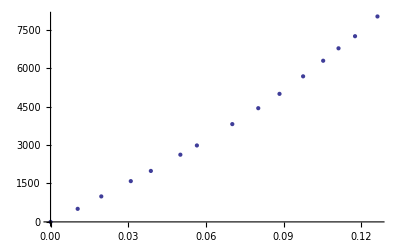

```mathematica
lp = ListPlot[data]
```

```mathematica
f3 = Fit[data, {x, x^2, x^3}, x]
```

49896.9 x+5154.98 x^2+814480. x^3

```mathematica
f3 /. x->0
```

0.

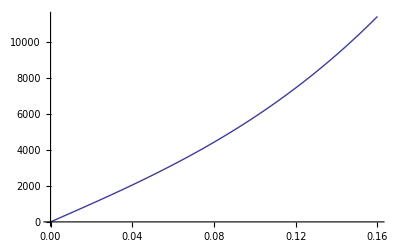

```mathematica
Plot[f3, {x, 0, 0.16}]
```

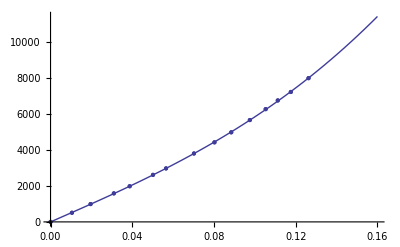

```mathematica
Show[%, lp]
```